```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/StocForm_for_Gauge/num"];
```

```mathematica
SgE=(e^3 B0)/(6 π^2)(E0^2/(E0^2+B0^2)Coth[π B0/E0]);
SgEp=(e^3 B0)/(12 π^2)(B0^2/(E0^2+B0^2)Coth[π B0/E0]+π B0/E0 Csch[π B0/E0]^2);
SgB=(e^3 E0)/(6 π^2)(B0^2/(E0^2+B0^2)Coth[π B0/E0]);
SgBp=(e^3 E0)/(12 π^2)(E0^2/(E0^2+B0^2)Coth[π B0/E0]-π B0/E0 Csch[π B0/E0]^2);
```

```mathematica
Limit[Coth[x],{x->∞}]
```

1

```mathematica
SgE/.{B0->10^3 E0}//N
SgEp/.{B0->10^3 E0}//N
```

0.0000168868 e^3 E0

General::munfl: Csch[3141.59] is too small to represent as a normalized machine number; precision may be lost.

8.44342 e^3 E0

```mathematica
SgB/.{B0->10E0}//N
SgBp/.{B0->10E0}//N
```

0.0167197 e^3 E0

0.0000835983 e^3 E0

```mathematica
2xi-1.2xi/.{xi->7}
```

5.6

```mathematica
E0sol[x_]=E0/.Solve[SgB+SgBp==2xi(*-xi/2*)/.{B0->x E0},E0][[1]]
```

(48 π^2 (xi+x^2 xi) Sinh[π x]^2)/(e^3 (-2 π x-2 π x^3+Sinh[2 π x]+2 x^2 Sinh[2 π x]))

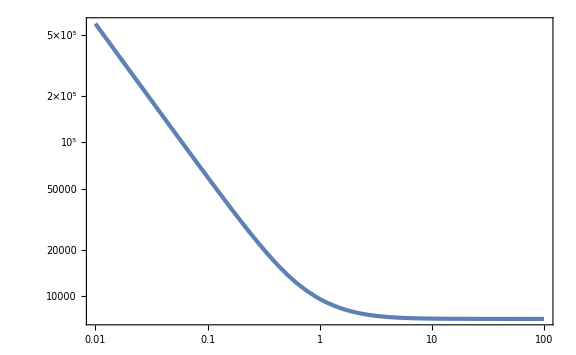

```mathematica
LogLogPlot[E0sol[x]/.{xi->10,e->0.55},{x,0.01,100}]
```

```mathematica
Limit[E0sol[x],{x->∞}]
```

(12 π^2 xi)/e^3

```mathematica
W[z_,xi_]=WhittakerW[-I xi,1/2,-2I z];
Wp[z_,xi_]=D[W[z,xi], z]//Simplify
WS[z_,xe_,Sigma_]=WhittakerW[-I xe,(1+Sigma)/2,-2I z]//Simplify
WSp[z_,xe_,Sigma_]=D[WS[z,xe,Sigma], z]//Simplify
MS[z_,xe_,Sigma_]=WhittakerM[-I xe,(1+Sigma)/2,-2I z]//Simplify
MSp[z_,xe_,Sigma_]=D[MS[z,xe,Sigma], z]//Simplify
```

(-WhittakerW[1-ⅈ xi,1/2,-2 ⅈ z]+ⅈ (xi-z) WhittakerW[-ⅈ xi,1/2,-2 ⅈ z])/z

WhittakerW[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]

(-WhittakerW[1-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]+ⅈ (xe-z) WhittakerW[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z])/z

WhittakerM[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]

((2+Sigma-2 ⅈ xe) WhittakerM[1-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]+2 ⅈ (xe-z) WhittakerM[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z])/(2 z)

### gamma = 2xieff

```mathematica
c1[xi_,xe_,Sigma_]=γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]MS[γ,xe,Sigma]-W[γ,xi]MSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]MS[γ,xe,Sigma])/.{γ->2xe}//Simplify;
c2[xi_,xe_,Sigma_]=-γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]WS[γ,xe,Sigma]-W[γ,xi]WSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]WS[γ,xe,Sigma])/.{γ->2xe}//Simplify;
```

```mathematica
Clear[PBBoH4,PEEoH4]
```

```mathematica
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma]]^2/;z<2xe
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[W[z,xi]]^2/;!(z<2xe)
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WSp[z,xe,Sigma]+c2[xi,xe,Sigma]MSp[z,xe,Sigma]+Sigma/(2z)(c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma])]^2/;z<2xe
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[Wp[z,xi]^2]/;!(z<2xe)
```

```mathematica
N[PBBoH4[1,5+1/2,5,4],30]
```

7973.61558354558003050130794792

```mathematica
ListPBBxp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEExp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.95361,Null}

{4.064,Null}

{2.79609,Null}

{5.24741,Null}

{2.26155,Null}

{5.70716,Null}

{2.88511,Null}

{7.71716,Null}

{2.61509,Null}

{8.52234,Null}

```mathematica
ListPBBSp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEESp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.31114,Null}

{6.0984,Null}

{1.90831,Null}

{5.67903,Null}

{2.24124,Null}

{2.86161,Null}

{2.17093,Null}

{4.95978,Null}

{2.17984,Null}

{5.21927,Null}

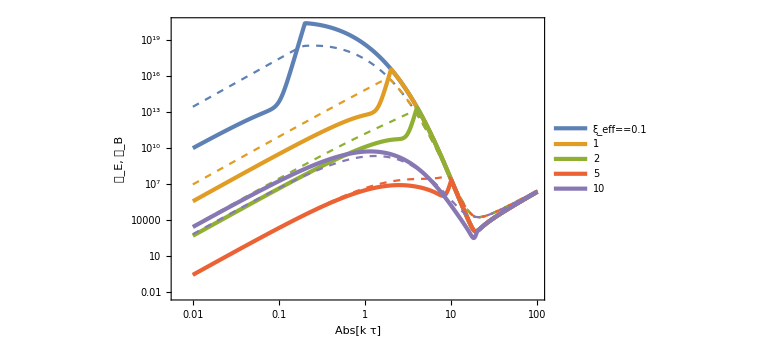

```mathematica
ListLogLogPlot[{ListPEExp1,ListPBBxp1,ListPEEx1,ListPBBx1,ListPEEx2,ListPBBx2,ListPEEx5,ListPBBx5,ListPEEx10,ListPBBx10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Subscript[ξ, eff]==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.7}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Σ==10}]}}]
```

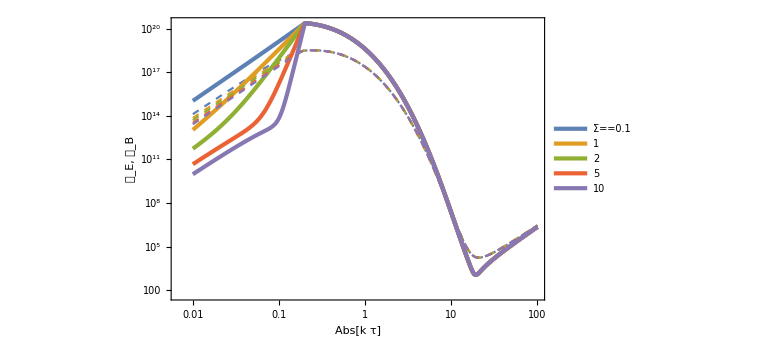

```mathematica
ListLogLogPlot[{ListPEESp1,ListPBBSp1,ListPEES1,ListPBBS1,ListPEES2,ListPBBS2,ListPEES5,ListPBBS5,ListPEES10,ListPBBS10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Σ==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.7}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Subscript[ξ, eff]==0.1}]}}]
```

### gamma = 2xi

```mathematica
c1[xi_,xe_,Sigma_]=γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]MS[γ,xe,Sigma]-W[γ,xi]MSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]MS[γ,xe,Sigma])/.{γ->2xi}//Simplify;
c2[xi_,xe_,Sigma_]=-γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]WS[γ,xe,Sigma]-W[γ,xi]WSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]WS[γ,xe,Sigma])/.{γ->2xi}//Simplify;
```

```mathematica
Clear[PBBoH4,PEEoH4]
```

```mathematica
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma]]^2/;z<2xi
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[W[z,xi]]^2/;!(z<2xi)
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WSp[z,xe,Sigma]+c2[xi,xe,Sigma]MSp[z,xe,Sigma]+Sigma/(2z)(c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma])]^2/;z<2xi
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[Wp[z,xi]^2]/;!(z<2xi)
```

```mathematica
N[PBBoH4[1,5+1/2,5,4],30]
```

4955.27782131228327958640544442

```mathematica
ListPBBxp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEExp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.15494,Null}

{5.08962,Null}

{1.87407,Null}

{7.34875,Null}

{2.32208,Null}

{6.31485,Null}

{2.47044,Null}

{7.72673,Null}

{2.24511,Null}

{7.81454,Null}

```mathematica
ListPBBSp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEESp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.7992,Null}

{4.47919,Null}

{2.12599,Null}

{5.27462,Null}

{2.52994,Null}

{4.32248,Null}

{2.14838,Null}

{3.60828,Null}

{2.25366,Null}

{4.05925,Null}

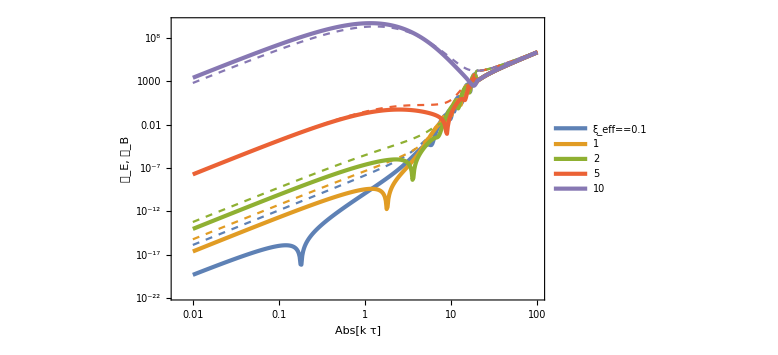

```mathematica
ListLogLogPlot[{ListPEExp1,ListPBBxp1,ListPEEx1,ListPBBx1,ListPEEx2,ListPBBx2,ListPEEx5,ListPBBx5,ListPEEx10,ListPBBx10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Subscript[ξ, eff]==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.3}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Σ==10, ", ", γ==2ξ}]}}]
```

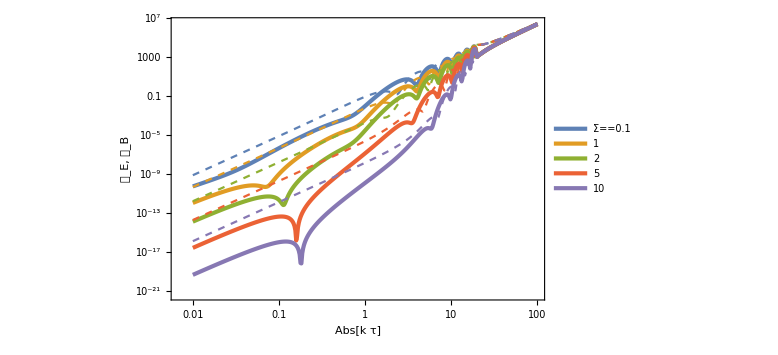

```mathematica
ListLogLogPlot[{ListPEESp1,ListPBBSp1,ListPEES1,ListPBBS1,ListPEES2,ListPBBS2,ListPEES5,ListPBBS5,ListPEES10,ListPBBS10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Σ==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.3}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Subscript[ξ, eff]==0.1, ", ",γ==2ξ}]}}]
```

```mathematica
consistentList=Sort[Import["c++/consistentEB.dat"]]
```

{{5,1400.1,756.78,1.75954,0.516006,0.951066,1.14852},{6,2150.08,1206.73,2.73447,0.803932,1.53473,1.77102},{7,2920.97,1711.8,3.76475,1.1155,2.20629,2.41173},{8,3680.86,2244.27,4.80042,1.43968,2.92688,3.03881},{9,4424.92,2784.46,5.82321,1.76967,3.66437,3.64688},{10,5139.49,3327.72,6.81697,2.10249,4.41386,4.22398},{11,5791.68,3917.58,7.77008,2.46423,5.25579,4.72839},{12,6544.38,4732.72,8.91845,2.98837,6.44959,5.25868},{13,7356.51,5573.3,10.1203,3.55377,7.66718,5.82198},{14,8127.39,6339.74,11.2397,4.07861,8.7675,6.3596}}

```mathematica
consistentE0=Table[{consistentList[[i,1]],consistentList[[i,2]]},{i,Length[consistentList]}];
consistentB0=Table[{consistentList[[i,1]],consistentList[[i,3]]},{i,Length[consistentList]}];
consistentSgE=Table[{consistentList[[i,1]],consistentList[[i,4]]},{i,Length[consistentList]}];
consistentSgEp=Table[{consistentList[[i,1]],consistentList[[i,5]]},{i,Length[consistentList]}];
consistentSgB=Table[{consistentList[[i,1]],consistentList[[i,6]]},{i,Length[consistentList]}];
consistentSgBp=Table[{consistentList[[i,1]],consistentList[[i,7]]},{i,Length[consistentList]}];
```

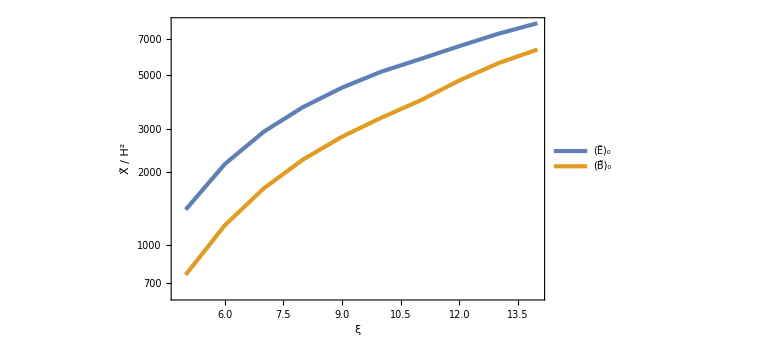

```mathematica
ListLogPlot[{consistentE0,consistentB0},FrameLabel->{ξ,Row[{OverTilde[X]," / ",H^2}]},PlotLegends->Placed[{Subscript[OverTilde["E"], 0],Subscript[OverTilde[B], 0]},{0.8,0.2}]]
```

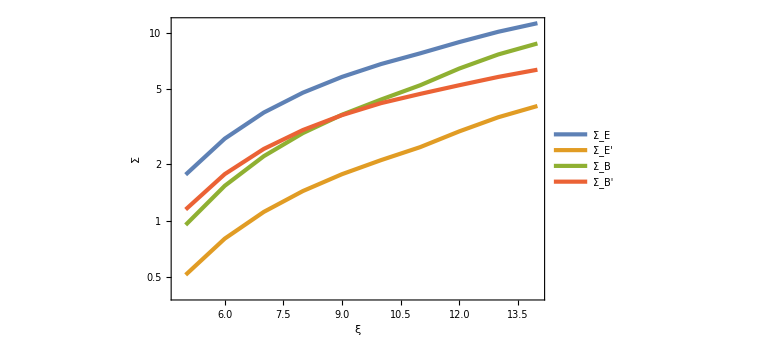

```mathematica
ListLogPlot[{consistentSgE,consistentSgEp,consistentSgB,consistentSgBp},FrameLabel->{ξ,Σ},PlotLegends->Placed[LineLegend[{Subscript[Σ, "E"],Subscript[Σ, "E"'],Subscript[Σ, B],Subscript[Σ, B']},LegendLayout->"Row"],{0.65,0.15}]]
```